Exercises for Section 34 | Associations

Make a list, in order, of the number of times each of the digits 0 through 9 occurs in 3^100. |

EXPECTED OUTPUT »

-Graphics- | ×

Enter code

```mathematica
IntegerDigits[3^100]
```

```mathematica
Values@KeySort[Counts[IntegerDigits[3^100]]]
```

{7,9,9,5,1,5,4,7,1}

Make a labeled bar chart of the number of times each of the digits 0 through 9 occurs in 2^1000. |

EXPECTED OUTPUT »

-Graphics- | ×

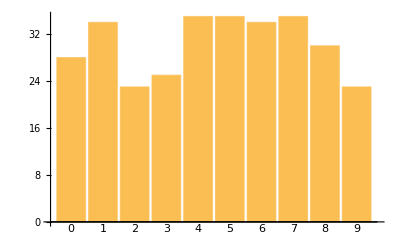

```mathematica
BarChart[KeySort@Counts[IntegerDigits[2^1000]],ChartLabels->Automatic]
```

Make a labeled bar chart of the number of times each possible first letter occurs in words from WordList[ ]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Take["x_"]&/@WordList[]
```

Take::normal: Nonatomic expression expected at position 1 in Take[x_,a].

Take::normal: Nonatomic expression expected at position 1 in Take[x_,aah].

Take::normal: Nonatomic expression expected at position 1 in Take[x_,aardvark].

General::stop: Further output of Take::normal will be suppressed during this calculation.

{Take[x_,a],Take[x_,aah],Take[x_,aardvark],Take[x_,aback],Take[x_,abacus],Take[x_,abaft],Take[x_,abalone],39163,Take[x_,zounds],Take[x_,zucchini],Take[x_,zwieback],Take[x_,zydeco],Take[x_,zygote],Take[x_,zygotic]}
 |  |  |  |

```mathematica
Characters["abcd"]
Take[Characters["abcd"],1]
```

{a,b,c,d}

{a}

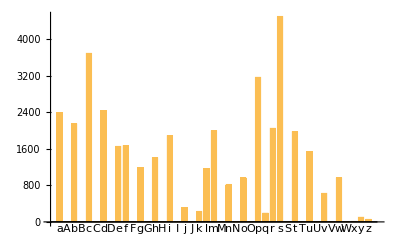

```mathematica
BarChart[KeySort@Counts@StringTake[WordList[],1],ChartLabels->Automatic]
```

Make an association giving the 5 most common first letters of words in WordList[ ] and their counts. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Normal[Counts[StringTake[WordList[],1]]][[1;;5]]
```

{a→2393,A→4,b→2146,B→1,c→3693}

```mathematica
TakeLargest[Counts[StringTake[WordList[],1]],5]
```

<|s→4499,c→3693,p→3168,d→2433,a→2393|>

Find the numerical ratio of the number of occurrences of “q” and “u” in the Wikipedia entry for computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Counts[Characters[WikipediaData["computers"]]]["q"]/Counts[Characters[WikipediaData["computers"]]]["u"]//N
```

0.0398693

```mathematica
((LetterCounts[WikipediaData["computers"]]["q"])/(LetterCounts[WikipediaData["computers"]]["u"]))//N
```

0.0398693

```mathematica
(*book answer, wiki info has since been updated. Numerical expected result differs. My program was correct*)
#q/#u &@LetterCounts[WikipediaData["computers"]] // N
```

0.0398693

```mathematica
()
```

0.0398693

Find the 10 most common words in ExampleData[{"Text","AliceInWonderland"}]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Keys[TakeLargest[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]],10]]
```

{the,and,a,to,she,of,was,Alice,in,it}